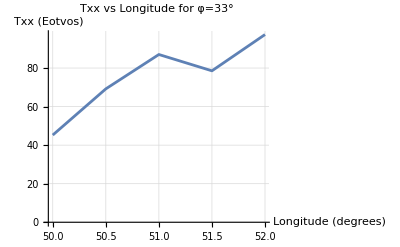

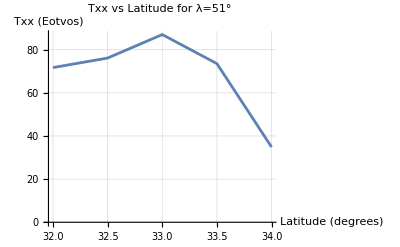

```mathematica
(*Load data from CSV file*)data=Import["D:\\programming\\Projects\\GeoGraphica\\GeoGraphicaPr\\sources\\final_phase\\all_sources\\project_result_csv_files\\mathematica\\MtxxTOTAL.csv","CSV"];

(*Extract longitude,latitude,and Txx values*)
longitude=ToExpression@data[[1,2;;]]; (*First row,excluding the first column*)
latitude=ToExpression@data[[2;;,1]]; (*First column,excluding the first row*)
TxxValues=ToExpression@data[[2;;,2;;]]; (*The remaining grid of Txx values*)

(*Plot Txx vs Longitude for φ=33°*)
phiFixed=33; (*Fixed latitude*)
phiIndex=First@FirstPosition[Abs[latitude-phiFixed],Min[Abs[latitude-phiFixed]]];
TxxVsLongitude=TxxValues[[phiIndex,All]];

ListLinePlot[Transpose[{longitude,TxxVsLongitude}],PlotLabel->"Txx vs Longitude for φ=33°",AxesLabel->{"Longitude (degrees)","Txx (Eotvos)"},PlotLegends->None,GridLines->Automatic]

(*Plot Txx vs Latitude for λ=51°*)
landaFixed=51; (*Fixed longitude*)
landaIndex=First@FirstPosition[Abs[longitude-landaFixed],Min[Abs[longitude-landaFixed]]];
TxxVsLatitude=TxxValues[[All,landaIndex]];

ListLinePlot[Transpose[{latitude,TxxVsLatitude}],PlotLabel->"Txx vs Latitude for λ=51°",AxesLabel->{"Latitude (degrees)","Txx (Eotvos)"},PlotLegends->None,GridLines->Automatic]
```